```mathematica
rawJSON=Import["http://repository.edition-topoi.org/BDIA/ReposBDIA/BDIA5012/FullDB.json","RawJSON"];
```

```mathematica
rawJSON=Import["/Users/christopher/Dropbox/brown/2019/asyrScience/finalProject/data/topoi/FullDB.json","RawJSON"];
```

```mathematica
Length[rawJSON]
```

377

```mathematica
tabletEvents=KeySelect[#,StringMatchQ["event-*"]]&/@rawJSON;
```

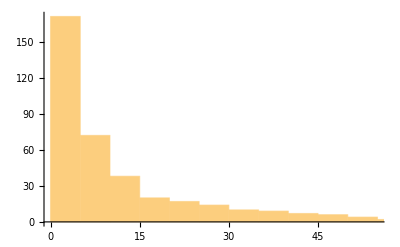

```mathematica
Histogram[Length/@tabletEvents]
```

```mathematica
allEvents=Catenate[Values/@tabletEvents];
```

```mathematica
Length[allEvents]
```

4363

```mathematica
<|
"j"->"julian year of the tablet name",
"m"->"julian month",
"rel2"->"{\"back_to_the_west\",\"high_to_the_north\",\"low_to_the_south\",\"passed_to_the_east\"} example line 4 -103 ",
"kusd20"->"kus + si with 20 si = 1 kus",
"balanced"->"see page 28 of I (the moon was balanced 1 cubit in front of Mars)",
"kus"->"relation 1 integer part of cubits?",
"obj2"->"secondary object",
"kus2d24"->Missing[],
"id"->"event ID",
"kusp2"->Missing[],
"day"->"babylonian day",
"number"->Missing[](*always the same as "id"*),
"kus2"->"relation 2 integer part of cubits?",
"shift"->Missing[](*always seems to be Null or shift*),
"event-type"->Missing[](*always "configuration"*),
"king"->"king of the reginal year",
"obj1"->"primary object",
"mjd"->Missing[](*Modified Julian Day but off by a few days (see allEvents[[11]])*),
"kusfrac2"->"relation 2 fractional part of cubits?",
"kusfrac"->"relation 1 fractional part of cubits?",
"kus2d20"->Missing[],
"kusd24"->"kus + si with 24 si = 1 kus",
"time"->"time of event"(*what is the difference between beginning_of_the_night and first_time_of_the_night?*),
"kusp"->Missing[](*always "kus" or Null*),
"type_filter_key"->Missing[](*always "configurartion" (like event-type)*),
"si2"->"fingers for relation 2",
"lfdnr"->"line number of the observation? Seems to be shifted by 1 from S&H",
"torel"->"position of event in the sky? (Always to the east or west)",
"month"->"babylonian month",
"rel"->"relationship {\"above\",\"behind\",\"below\",\"in_front_of\",\"is_standing_in\"}",
"year_filter_key"->Missing[](*always the same as "year"*),
"table"->"some sort of tablet ID",
"si"->"fingers",
"sip"->Missing[](*whether the word used for "fingers" was "si" or "u"?*),
"sip2"->Missing[](*same as sip*),
"t"->"julian day",
"type"->Missing[](*always "event"*),
"year"->"babylonian reginal year together with \"king\""
|>
```

```mathematica
FromJulianDate["Modified",-716686]
```

Thu 27 Aug -105 20:00:00GMT-4.

```mathematica
allEvents[[11,{"mjd","j","m","t","year","month","day"}]]
```

<|mjd→-716686,j→-104,m→8,t→31,year→207,month→6,day→3|>

kus and kus2 are for cubits, si and si2 are for fingers?

```mathematica
Select[allEvents,#sip==="u"&]//Length
```

72

```mathematica
N[#kus+If[#kusfrac===Null,0,ToExpression[#kusfrac]]+If[#si===Null,0,#si/20]]==#kusd20&@<|"j"->-103,"m"->4,"rel2"->"low_to_the_south","kusd20"->1.5,"balanced"->Null,"kus"->1,"obj2"->"th_leonis","kus2d24"->4.5,"id"->5442,"kusp2"->"kus","day"->8,"number"->5442,"kus2"->4,"shift"->"shift","event-type"->"configuration","king"->"seleucid_era","obj1"->"moon","mjd"->-716444,"kusfrac2"->"1 / 2","kusfrac"->"1 / 2","kus2d20"->4.5,"kusd24"->1.5,"time"->"beginning_of_night","kusp"->"kus","type_filter_key"->"configuration","si2"->Null,"lfdnr"->3,"torel"->Null,"month"->2,"rel"->"behind","year_filter_key"->208,"table"->"pl103A","si"->Null,"sip"->Null,"sip2"->Null,"t"->30,"type"->"event","year"->208|>
```

True

```mathematica
Select[allEvents,#kus=!=Null&&N[#kus+If[#kusfrac===Null,0,ToExpression[#kusfrac]]+If[#si===Null,0,#si/20]]-#kusd20<0.001&][[1]]
```

<|j→-103,m→4,rel2→low_to_the_south,kusd20→1.5,balanced→Null,kus→1,obj2→th_leonis,kus2d24→4.5,id→5442,kusp2→kus,day→8,number→5442,kus2→4,shift→shift,event-type→configuration,king→seleucid_era,obj1→moon,mjd→-716444,kusfrac2→1 / 2,kusfrac→1 / 2,kus2d20→4.5,kusd24→1.5,time→beginning_of_night,kusp→kus,type_filter_key→configuration,si2→Null,lfdnr→3,torel→Null,month→2,rel→behind,year_filter_key→208,table→pl103A,si→Null,sip→Null,sip2→Null,t→30,type→event,year→208|>

```mathematica
Select[allEvents,#si=!=Null&][[All,"si"]]
```

{6,8,6,20,6,20,4,4,6,8,2,6,20,20,6,6,20,6,8,2,8,4,4,20,2,6,10,20,1,4,4,6,1,4,6,6,8,8,20,4,1,4,2,8,4,2,6,2,6,2,10,8,10,10,6,4,4,20,4,6,2,5,4,8,6,8,6,8,8,8,8,8,4,8,10,4,4,10,2,20,18,2,8,2,2,2,2,1,2,4,4,2,10,2,5,6,2,2,3,20,8,2,8,4,2,4,4,2,4,8,10,2,21,4,5,8,6,8,4,2,4,20,8,1,2,6,6,4,4,6,6,3,2,10,6,4,20,8,8,1,6,4,4,4,4,1,8,8,8,10,8,10,8,6,8,10,6,6,4,3,1,2,4,4,4,8,4,8,1,2,2,1,5,6,20,8,4,18,4,8,8,8,4,8,4,8,6,6,4,8,2,8,8,8,14,8,8,8,8,3,8,1,1,8,4,8,4,6,4,2,14,20,4,2,4,8,10,8,8,5,6,6,1,4,8,4,8,4,6,8,14,20,2,8,10,3,4,4,8,8,8,20,1,4,8,4,2,8,10,3,8,8,8,8,8,3,8,4,8,2,8,8,8,8,4,4,8,8,4,14,8,8,6,8,8,1,8,8,4,8,8,8,8,8,20,8,8,20,8,8,3,4,6,14,1,20,10,8,20,18,8,20,20,2,6,8,4,20,18,2,20,5,20,20,4,4,20,8,8,8,8,20,6,8,8,20,4,8,20,8,8,20,8,8,8,8,20,20,8,20,8,14,8,8,2,8,4,8,3,8,10,8,8,8,8,18,6,8,8,8,20,8,6,8,14,4,8,3,4}

```mathematica
Complement[Select[allEvents,#si=!=Null&],Select[allEvents,#kusd20=!=#kusd24&]]
```

{<|j→-144,m→9,rel2→Null,kusd20→Null,balanced→Null,kus→Null,obj2→r_leonis,kus2d24→Null,id→3746,kusp2→Null,day→24,number→3746,kus2→Null,shift→Null,event-type→configuration,king→seleucid_era,obj1→moon,mjd→-731282,kusfrac2→Null,kusfrac→Null,kus2d20→Null,kusd24→Null,time→last_part_of_night,kusp→Null,type_filter_key→configuration,si2→Null,lfdnr→11,torel→Null,month→6,rel→in_front_of,year_filter_key→167,table→pl144A,si→2,sip→Null,sip2→Null,t→14,type→event,year→167|>,<|j→-144,m→9,rel2→Null,kusd20→Null,balanced→Null,kus→Null,obj2→z_tauri,kus2d24→Null,id→3741,kusp2→Null,day→18,number→3741,kus2→Null,shift→Null,event-type→configuration,king→seleucid_era,obj1→moon,mjd→-731288,kusfrac2→Null,kusfrac→Null,kus2d20→Null,kusd24→Null,time→last_part_of_night,kusp→kus,type_filter_key→configuration,si2→Null,lfdnr→6,torel→Null,month→6,rel→in_front_of,year_filter_key→167,table→pl144A,si→18,sip→si,sip2→Null,t→8,type→event,year→167|>}

```mathematica
allEvents[[1]]
```

<|j→-103,m→4,rel2→low_to_the_south,kusd20→1.5,balanced→Null,kus→1,obj2→th_leonis,kus2d24→4.5,id→5442,kusp2→kus,day→8,number→5442,kus2→4,shift→shift,event-type→configuration,king→seleucid_era,obj1→moon,mjd→-716444,kusfrac2→1 / 2,kusfrac→1 / 2,kus2d20→4.5,kusd24→1.5,time→beginning_of_night,kusp→kus,type_filter_key→configuration,si2→Null,lfdnr→3,torel→Null,month→2,rel→behind,year_filter_key→208,table→pl103A,si→Null,sip→Null,sip2→Null,t→30,type→event,year→208|>

```mathematica
Union@allEvents[[All,"si"]]
```

{1,2,3,4,5,6,8,10,14,18,20,21,Null}

```mathematica
Select[allEvents,#sip==="u"&]
```

```mathematica
DateObject[{-103,4,30},CalendarType->"Julian"]+Quantity[844208,"Day"]
```

Day: Thu 23 Aug 2209 (Juliancalendar)

```mathematica
dates=DateObject[Lookup[#,{"j","m","t"}],CalendarType->"Julian"]&/@allEvents;
```

```mathematica
Union@Select[dates-QuantityArray[allEvents[[All,"mjd"]],"Days"],DateObjectQ]
```

{Day: Thu 5 Nov 1859 (Juliancalendar),Day: Fri 6 Nov 1859 (Juliancalendar)}

```mathematica
Differences@dates
```

{2 days,8 days,6 days,2 days,0,0,-9 days,16 days,DateObject[{Null,Null,Null},CalendarType→Julian]-Day: Sun 25 May -103 (Juliancalendar),-DateObject[{Null,Null,Null},CalendarType→Julian]+Day: Sat 31 Aug -104 (Juliancalendar),1 day,1 day,0,0,3 days,-502 days,3 days,1 day,2 days,1 day,0,1 day,0,3 days}

```mathematica
Differences@allEvents[[;;25,"mjd"]]
```

{2,8,6,2,0,0,-9,16,716419+Null,-716686-Null,1,1,0,0,3,-503,3,1,2,1,0,1,0,3}

```mathematica
dates
```

{Day: Wed 30 Apr -103 (Juliancalendar),Day: Fri 2 May -103 (Juliancalendar),Day: Sat 10 May -103 (Juliancalendar),Day: Fri 16 May -103 (Juliancalendar),Day: Sun 18 May -103 (Juliancalendar),Day: Sun 18 May -103 (Juliancalendar),Day: Sun 18 May -103 (Juliancalendar),Day: Fri 9 May -103 (Juliancalendar),Day: Sun 25 May -103 (Juliancalendar)}

```mathematica
Union@allEvents[[All,"mjd"]]
```

```mathematica
alLE
```

```mathematica
allEvents[[2,"t"]]
```

2

```mathematica
Union@allEvents[[All,"year"]]
```

{1,2,3,4,5,7,8,9,11,12,15,16,17,18,20,22,23,24,25,26,27,28,29,30,31,32,33,34,35,37,38,41,43,45,47,48,49,50,51,52,54,55,56,57,58,60,62,64,65,66,69,70,71,72,73,74,77,79,81,82,84,85,86,89,90,93,98,99,100,101,102,104,107,108,109,110,111,112,113,114,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,138,140,141,142,143,144,145,146,147,148,149,150,151,153,154,155,156,157,158,159,160,162,163,165,167,168,169,170,171,174,175,176,177,178,179,180,181,182,185,186,187,188,189,190,191,192,193,194,199,200,201,202,203,204,205,206,207,208,Null}

```mathematica
Counts@allEvents[[All,"event-type"]]
```

<|configuration→4363|>

```mathematica
ReverseSort@Counts@allEvents[[All,"si"]]
```

<|Null→3994,8→123,4→68,6→42,2→38,20→36,10→17,1→16,3→10,14→7,5→6,18→5,21→1|>

```mathematica
KeySort@Counts@allEvents[[All,"j"]]
```

<|-453→1,-418→9,-417→1,-384→3,-383→3,-382→9,-381→10,-379→4,-378→8,-375→1,-374→20,-373→9,-372→31,-371→5,-366→31,-346→16,-345→34,-342→6,-333→8,-332→21,-329→3,-328→15,-324→72,-322→15,-321→80,-309→4,-308→30,-307→6,-302→3,-300→13,-299→1,-294→2,-293→6,-291→33,-289→25,-288→18,-287→10,-286→7,-284→25,-283→9,-281→6,-280→12,-278→6,-277→77,-275→2,-273→36,-272→16,-270→18,-269→6,-266→19,-264→3,-263→2,-262→13,-261→12,-260→3,-257→1,-256→2,-255→52,-254→5,-253→47,-252→5,-251→25,-250→19,-249→6,-248→17,-247→6,-246→49,-245→24,-241→6,-239→3,-238→1,-237→37,-234→36,-233→13,-232→38,-231→39,-230→14,-229→5,-228→1,-226→19,-225→36,-221→13,-220→1,-218→19,-217→3,-213→3,-212→1,-211→15,-210→30,-209→55,-207→25,-204→2,-203→1,-202→22,-201→1,-200→3,-199→7,-198→12,-197→24,-196→33,-195→21,-194→33,-193→28,-192→20,-191→27,-190→36,-189→2,-188→2,-187→18,-186→8,-185→24,-184→2,-183→22,-182→19,-181→32,-179→21,-178→10,-177→13,-176→8,-175→4,-173→19,-172→15,-171→2,-170→56,-169→4,-168→40,-166→3,-165→8,-164→22,-163→51,-162→57,-161→61,-160→2,-159→1,-158→51,-157→16,-156→48,-155→19,-154→8,-153→11,-151→2,-149→13,-148→2,-145→8,-144→65,-143→39,-142→9,-141→40,-140→92,-139→47,-137→47,-136→51,-135→17,-134→22,-133→28,-132→128,-131→11,-130→12,-129→48,-125→25,-124→80,-123→71,-122→36,-121→10,-120→11,-119→45,-118→44,-117→7,-116→11,-112→3,-111→54,-110→12,-109→19,-108→57,-107→43,-106→22,-105→124,-104→6,-103→9,Null→535|>

```mathematica
Union@allEvents[[All,"mjd"]]
```

```mathematica
Union@allEvents[[All,"obj1"]]
```

{jupiter,mars,mercury,moon,saturn,venus}

```mathematica
Union@allEvents[[All,"obj2"]]
```

{a_arietis,a_geminorum,a_leonis,a_librae,aquarius,aries,a_scorpii,a_tauri,a_virginis,b_arietis,b_capricorni,b_geminorum,b_librae,b_scorpii,b_tauri,b_virginis,cancer,capricorn,d_cancri,d_capricorni,d_scorpii,e_cancri,e_geminorum,electra,e_piscium,eps_leonis,g_cancri,g_capricorni,gemini,g_geminorum,g_virginis,jupiter,leo,libra,mars,mercury,m_geminorum,moon,pisces,p_scorpii,r_leonis,sagittarius,saturn,scorpius,taurus,th_cancri,th_leonis,th_ophiuchi,venus,virgo,z_tauri}

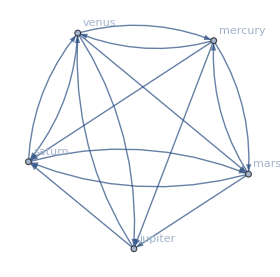

```mathematica
Subgraph[Graph[DeleteDuplicates[DirectedEdge@@@Values@allEvents[[All,{"obj1","obj2"}]]],VertexLabels->"Name"],{"mars","jupiter","saturn","mercury","venus"}]
```

```mathematica
allEvents[[;;5]]
```

{<|j→-103,m→4,rel2→low_to_the_south,kusd20→1.5,balanced→Null,kus→1,obj2→th_leonis,kus2d24→4.5,id→5442,kusp2→kus,day→8,number→5442,kus2→4,shift→shift,event-type→configuration,king→seleucid_era,obj1→moon,mjd→-716444,kusfrac2→1 / 2,kusfrac→1 / 2,kus2d20→4.5,kusd24→1.5,time→beginning_of_night,kusp→kus,type_filter_key→configuration,si2→Null,lfdnr→3,torel→Null,month→2,rel→behind,year_filter_key→208,table→pl103A,si→Null,sip→Null,sip2→Null,t→30,type→event,year→208|>,<|j→-103,m→5,rel2→high_to_the_north,kusd20→2.,balanced→Null,kus→2,obj2→g_virginis,kus2d24→3.,id→5443,kusp2→kus,day→10,number→5443,kus2→3,shift→shift,event-type→configuration,king→seleucid_era,obj1→moon,mjd→-716442,kusfrac2→Null,kusfrac→Null,kus2d20→3.,kusd24→2.,time→beginning_of_night,kusp→kus,type_filter_key→configuration,si2→Null,lfdnr→4,torel→Null,month→2,rel→behind,year_filter_key→208,table→pl103A,si→Null,sip→Null,sip2→Null,t→2,type→event,year→208|>,<|j→-103,m→5,rel2→Null,kusd20→1.,balanced→Null,kus→1,obj2→g_capricorni,kus2d24→Null,id→5445,kusp2→Null,day→18,number→5445,kus2→Null,shift→Null,event-type→configuration,king→seleucid_era,obj1→moon,mjd→-716434,kusfrac2→Null,kusfrac→Null,kus2d20→Null,kusd24→1.,time→last_part_of_night,kusp→kus,type_filter_key→configuration,si2→Null,lfdnr→7,torel→Null,month→2,rel→in_front_of,year_filter_key→208,table→pl103A,si→Null,sip→Null,sip2→Null,t→10,type→event,year→208|>,<|j→-103,m→5,rel2→passed_to_the_east,kusd20→6.,balanced→Null,kus→6,obj2→b_arietis,kus2d24→Null,id→5446,kusp2→a_little,day→24,number→5446,kus2→Null,shift→shift,event-type→configuration,king→seleucid_era,obj1→moon,mjd→-716428,kusfrac2→Null,kusfrac→Null,kus2d20→Null,kusd24→6.,time→last_part_of_night,kusp→kus,type_filter_key→configuration,si2→Null,lfdnr→8,torel→Null,month→2,rel→below,year_filter_key→208,table→pl103A,si→Null,sip→Null,sip2→Null,t→16,type→event,year→208|>,<|j→-103,m→5,rel2→low_to_the_south,kusd20→1.,balanced→Null,kus→1,obj2→venus,kus2d24→2.,id→5447,kusp2→kus,day→26,number→5447,kus2→2,shift→shift,event-type→configuration,king→seleucid_era,obj1→moon,mjd→-716426,kusfrac2→Null,kusfrac→Null,kus2d20→2.,kusd24→1.,time→last_part_of_night,kusp→kus,type_filter_key→configuration,si2→Null,lfdnr→9,torel→Null,month→2,rel→in_front_of,year_filter_key→208,table→pl103A,si→Null,sip→Null,sip2→Null,t→18,type→event,year→208|>}